```mathematica
subs:={omega0->Sqrt[k/m],zeta->c/(2*Sqrt[m*k]),x0->-g*m/k}
```

```mathematica
xt=A*Exp[-zeta*omega0*t]*Sin[Sqrt[1-zeta^2]*omega0*t+phi]-g/omega0^2
```

-g/omega0^2+A ⅇ^(-omega0 t zeta) Sin[phi+omega0 t √(1-zeta^2)]

```mathematica
vt=FullSimplify[D[xt,t]]
```

A ⅇ^(-omega0 t zeta) omega0 (√(1-zeta^2) Cos[phi+omega0 t √(1-zeta^2)]-zeta Sin[phi+omega0 t √(1-zeta^2)])

```mathematica
energy=(m*g*x+k*x^2/2+m*v^2/2 == m*g*(x0-A)+k*(x0-A)^2/2 )/.subs
```

(m v^2)/2+g m x+(k x^2)/2==g m (-A-(g m)/k)+1/2 k (-A-(g m)/k)^2

```mathematica
Solve[energy,A]
```

{{A→-(√(g^2 m^2+k m v^2+2 g k m x+k^2 x^2))/k},{A→(√(g^2 m^2+k m v^2+2 g k m x+k^2 x^2))/k}}

```mathematica
amplitude=(√(k m v^2+(g m+k x)^2))/k
```

(√(k m v^2+(g m+k x)^2))/k

```mathematica
getphi[A_,isUp_]:=If[isUp,ArcSin[(x+g/omega0^2)/A],π-ArcSin[(x+g/omega0^2)/A]]
```

```mathematica
experiment:={g->9.8,m->3,k->2,c->0.3}
```

```mathematica
initials:={x->-5,v->3}
```

```mathematica
amplitude/.experiment/.initials
```

10.3726

```mathematica
getphi[amplitude/.experiment/.initials,True]/.subs/.experiment/.initials
```

1.20871

```mathematica
Minimize[{((xt+5)^2+(vt-3)^2)/.subs/.experiment/.{t->0},A>0},{A,phi}]
```

{0.,{A→10.6008,phi→1.15558}}

```mathematica
{xt==-5,vt==3,A>0}/.subs/.experiment/.initials
```

{-14.7+A ⅇ^(-0.05 t) Sin[phi+0.814964 t]==-5,√(2/3) A ⅇ^(-0.05 t) (0.998123 Cos[phi+0.814964 t]-0.0612372 Sin[phi+0.814964 t])==3,A>0}

```mathematica
Solve[{xt==-5,vt==3,A>0,phi≥0,phi<2*π}/.subs/.experiment/.initials/.{t->0},{A,phi}]
```

{{A→10.6008,phi→1.15558}}

```mathematica
xt/.subs/.{t->0}
```

-(g m)/k+A Sin[phi]

```mathematica
vt/.subs/.{t->0}
```

A √(k/m) (√(1-c^2/(4 k m)) Cos[phi]-(c Sin[phi])/(2 √(k m)))

```mathematica
Solve[{xt==x,vt==v,A>0,phi≥0,phi<2*π}/.subs/.experiment/.{t->0},{A,phi}]
```

$Aborted

```mathematica
xt/.subs/.experiment/.{A->10.60077410113466,phi->1.155576128610492,t->0}
```

-5.

```mathematica
vt/.subs/.experiment/.{A->10.60077410113466,phi->1.155576128610492,t->0}
```

3.

```mathematica
xt/.subs/.{t->0}
```

-(g m)/k+A Sin[phi]

```mathematica
FullSimplify[vt/.subs/.{t->0}]
```

A √(k/m) (√(1-c^2/(4 k m)) Cos[phi]-(c Sin[phi])/(2 √(k m)))

```mathematica
Solve[{-(g m)/k+A Sin[phi]==x,A √(k/m) (√(1-c^2/(4 k m)) Cos[phi]-(c Sin[phi])/(2 √(k m)))==v,g≥0,k>0,m>0,c≥0},{A,phi}]
```

```mathematica
FullSimplify[Solve[-g*m/k+(√(k m v^2+(g m+k x)^2))/k*Sin[phi]==x,phi]]
```

{{phi→ConditionalExpression[π-ArcSin[(g m+k x)/(√(k m v^2+(g m+k x)^2))]+2 π C[1],C[1]∈Integers]},{phi→ConditionalExpression[ArcSin[(g m+k x)/(√(k m v^2+(g m+k x)^2))]+2 π C[1],C[1]∈Integers]}}

```mathematica
{{phi->ConditionalExpression[π-ArcSin[(g m+k x)/(√(k m v^2+(g m+k x)^2))]+2 π C[1],C[1]∈Integers]},{phi->ConditionalExpression[ArcSin[(g m+k x)/(√(k m v^2+(g m+k x)^2))]+2 π C[1],C[1]∈Integers]}}/.experiment/.initials
```

{{phi→ConditionalExpression[1.93288+2 π C[1],C[1]∈Integers]},{phi→ConditionalExpression[1.20871+2 π C[1],C[1]∈Integers]}}

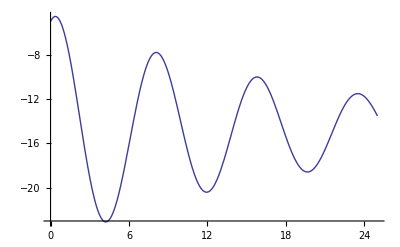

```mathematica
Plot[xt/.subs/.experiment/.{A->10.372559954032564,phi->1.2087096232338574},{t,0,25}]
```

```mathematica
(x''[t]+2*zeta*omega0*x'[t]+omega0^2*x[t]==-g)/.subs
```

(k x[t])/m+(c √(k/m) x'[t])/(√(k m))+x''[t]==-g

```mathematica
DSolve[{(x''[t]+2*zeta*omega0*x'[t]+omega0^2*x[t]==-g)/.subs},x[t],t]
```

{{x[t]→-(g m)/k+ⅇ^(((-c √(k/m) m-√k √m √(c^2-4 k m)) t)/(2 m √(k m))) C[1]+ⅇ^(((-c √(k/m) m+√k √m √(c^2-4 k m)) t)/(2 m √(k m))) C[2]}}

```mathematica
DSolve[{(x''[t]+2*zeta*omega0*x'[t]+omega0^2*x[t]==-g)/.subs,x'[0]==v1,x[0]==x1},x[t],t]//FullSimplify
```

{{x[t]→1/(2 k^(3/2) √(c^2-4 k m))ⅇ^(-((c √(k/m) √m+√k √(c^2-4 k m)) t)/(2 √m √(k m))) (c (-1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) √(k/m) √m (g m+k x1)+√k ((1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))-2 ⅇ^(((c √(k/m) √m+√k √(c^2-4 k m)) t)/(2 √m √(k m)))) g m √(c^2-4 k m)+2 (-1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) √k √m √(k m) v1+(1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) k √(c^2-4 k m) x1))}}

```mathematica
(1/(2 k^(3/2) √(c^2-4 k m))ⅇ^(-((c √(k/m) √m+√k √(c^2-4 k m)) t)/(2 √m √(k m))) (c (-1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) √(k/m) √m (g m+k x1)+√k ((1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))-2 ⅇ^(((c √(k/m) √m+√k √(c^2-4 k m)) t)/(2 √m √(k m)))) g m √(c^2-4 k m)+2 (-1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) √k √m √(k m) v1+(1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) k √(c^2-4 k m) x1)))/.experiment/.{x1->-5,v1->3,t->0}
```

-5.+0. ⅈ

```mathematica
newsol:=1/(2 k^(3/2) √(c^2-4 k m))ⅇ^(-((c √(k/m) √m+√k √(c^2-4 k m)) t)/(2 √m √(k m))) (c (-1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) √(k/m) √m (g m+k x1)+√k ((1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))-2 ⅇ^(((c √(k/m) √m+√k √(c^2-4 k m)) t)/(2 √m √(k m)))) g m √(c^2-4 k m)+2 (-1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) √k √m √(k m) v1+(1+ⅇ^((√(k m) √(c^2-4 k m) t)/(√k m^(3/2)))) k √(c^2-4 k m) x1))
```

```mathematica
FullSimplify[DSolve[{(x''[t]+2*zeta*omega0*x'[t]+omega0^2*x[t]==-g)/.subs,x'[0]==v1,x[0]==x1},x[t],t],{Element[t,Reals],Element[v1,Reals],Element[x1,Reals],Element[m,Reals],Element[g,Reals],Element[c,Reals],Element[k,Reals],m>0,g>0,c≥0,k>0}]
```

{{x[t]→(ⅇ^(-((c+√(c^2-4 k m)) t)/(2 m)) ((1+ⅇ^((√(c^2-4 k m) t)/m)-2 ⅇ^(((c+√(c^2-4 k m)) t)/(2 m))) g m √(c^2-4 k m)+c (-1+ⅇ^((√(c^2-4 k m) t)/m)) (g m+k x1)+k (2 (-1+ⅇ^((√(c^2-4 k m) t)/m)) m v1+(1+ⅇ^((√(c^2-4 k m) t)/m)) √(c^2-4 k m) x1)))/(2 k √(c^2-4 k m))}}

```mathematica
news:=(ⅇ^(-((c+√(c^2-4 k m)) t)/(2 m)) ((1+ⅇ^((√(c^2-4 k m) t)/m)-2 ⅇ^(((c+√(c^2-4 k m)) t)/(2 m))) g m √(c^2-4 k m)+c (-1+ⅇ^((√(c^2-4 k m) t)/m)) (g m+k x1)+k (2 (-1+ⅇ^((√(c^2-4 k m) t)/m)) m v1+(1+ⅇ^((√(c^2-4 k m) t)/m)) √(c^2-4 k m) x1)))/(2 k √(c^2-4 k m))
```

```mathematica
news/.experiment/.{x1->-5,v1->3,t->0}
```

-5.+0. ⅈ

```mathematica
Simplify[ExpToTrig[news]]
```

1/(2 k √(c^2-4 k m))(Cosh[((c+√(c^2-4 k m)) t)/(2 m)]-Sinh[((c+√(c^2-4 k m)) t)/(2 m)]) (-c g m+g m √(c^2-4 k m)-2 k m v1-c k x1+k √(c^2-4 k m) x1+(c g m+g m √(c^2-4 k m)+2 k m v1+c k x1+k √(c^2-4 k m) x1) Cosh[(√(c^2-4 k m) t)/m]-2 g m √(c^2-4 k m) Cosh[((c+√(c^2-4 k m)) t)/(2 m)]+c g m Sinh[(√(c^2-4 k m) t)/m]+g m √(c^2-4 k m) Sinh[(√(c^2-4 k m) t)/m]+2 k m v1 Sinh[(√(c^2-4 k m) t)/m]+c k x1 Sinh[(√(c^2-4 k m) t)/m]+k √(c^2-4 k m) x1 Sinh[(√(c^2-4 k m) t)/m]-2 g m √(c^2-4 k m) Sinh[((c+√(c^2-4 k m)) t)/(2 m)])

```mathematica
FullSimplify[news]
```

(ⅇ^(-((c+√(c^2-4 k m)) t)/(2 m)) ((1+ⅇ^((√(c^2-4 k m) t)/m)-2 ⅇ^(((c+√(c^2-4 k m)) t)/(2 m))) g m √(c^2-4 k m)+c (-1+ⅇ^((√(c^2-4 k m) t)/m)) (g m+k x1)+k (2 (-1+ⅇ^((√(c^2-4 k m) t)/m)) m v1+(1+ⅇ^((√(c^2-4 k m) t)/m)) √(c^2-4 k m) x1)))/(2 k √(c^2-4 k m))

```mathematica
news/.{√(c^2-4 k m)->p,x1->x,v1->v}
```

(ⅇ^(-((c+p) t)/(2 m)) ((1+ⅇ^((p t)/m)-2 ⅇ^(((c+p) t)/(2 m))) g m p+c (-1+ⅇ^((p t)/m)) (g m+k x)+k (2 (-1+ⅇ^((p t)/m)) m v+(1+ⅇ^((p t)/m)) p x)))/(2 k √(c^2-4 k m))

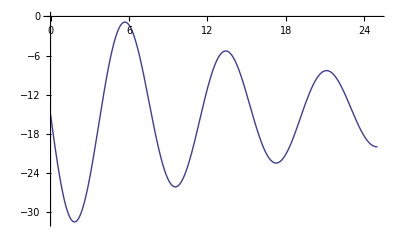

```mathematica
Plot[news/.experiment/.{x1->-15,v1->-15},{t,0,25}]
```

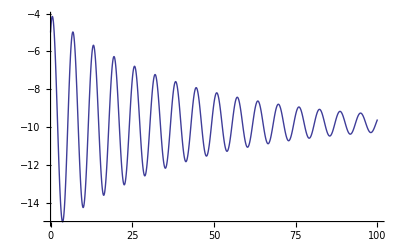

```mathematica
Plot[news/.{g->9.8,m->2,k->2,c->0.1}/.{x1->-5,v1->3},{t,0,100},PlotRange->All]
```

```mathematica
news/.{g->9.8,m->3,k->2,c->4}/.{x1->-5,v1->3}//FullSimplify
```

-14.7+ⅇ^(-1/3 (2+ⅈ √2) t) ((4.85+10.0409 ⅈ)+(4.85-10.0409 ⅈ) ⅇ^(2/3 ⅈ √2 t))

```mathematica
FullSimplify[DSolve[{(x''[t]+2*zeta*omega0*x'[t]+omega0^2*x[t]==-g)/.subs,x'[0]==v1,x[0]==x1},x[t],t],{Element[t,Reals],Element[v1,Reals],Element[x1,Reals],Element[m,Reals],Element[g,Reals],Element[c,Reals],Element[k,Reals],m>0,g>0,c≥0,k>0,c^2<4*k*m}]
```

{{x[t]→(ⅇ^(-((c+ⅈ √(-c^2+4 k m)) t)/(2 m)) (ⅈ (1+ⅇ^((ⅈ √(-c^2+4 k m) t)/m)-2 ⅇ^(((c+ⅈ √(-c^2+4 k m)) t)/(2 m))) g m √(k (-c^2+4 k m))-2 k^(3/2) m v1+2 ⅇ^((ⅈ √(-c^2+4 k m) t)/m) k^(3/2) m v1+ⅈ √(k^3 (-c^2+4 k m)) x1+ⅈ ⅇ^((ⅈ √(-c^2+4 k m) t)/m) √(k^3 (-c^2+4 k m)) x1+c (-1+ⅇ^((ⅈ √(-c^2+4 k m) t)/m)) √k (g m+k x1)))/(2 k^(3/2) √(c^2-4 k m))}}

```mathematica
FullSimplify[TrigReduce[ExpToTrig[(ⅇ^(-((c+ⅈ √(-c^2+4 k m)) t)/(2 m)) (ⅈ (1+ⅇ^((ⅈ √(-c^2+4 k m) t)/m)-2 ⅇ^(((c+ⅈ √(-c^2+4 k m)) t)/(2 m))) g m √(k (-c^2+4 k m))-2 k^(3/2) m v1+2 ⅇ^((ⅈ √(-c^2+4 k m) t)/m) k^(3/2) m v1+ⅈ √(k^3 (-c^2+4 k m)) x1+ⅈ ⅇ^((ⅈ √(-c^2+4 k m) t)/m) √(k^3 (-c^2+4 k m)) x1+c (-1+ⅇ^((ⅈ √(-c^2+4 k m) t)/m)) √k (g m+k x1)))/(2 k^(3/2) √(c^2-4 k m))]]]
```

$Aborted

```mathematica
ExpToTrig[Exp[Sqrt[-1]*x]]
```

```mathematica
ExpToTrig[Exp[Sqrt[-1]*x]]
```

Cos[x]+ⅈ Sin[x]

```mathematica
TraditionalForm[Style[(ⅇ^(-((c+ⅈ √(-c^2+4 k m)) t)/(2 m)) (ⅈ (1+ⅇ^((ⅈ √(-c^2+4 k m) t)/m)-2 ⅇ^(((c+ⅈ √(-c^2+4 k m)) t)/(2 m))) g m √(k (-c^2+4 k m))-2 k^(3/2) m v1+2 ⅇ^((ⅈ √(-c^2+4 k m) t)/m) k^(3/2) m v1+ⅈ √(k^3 (-c^2+4 k m)) x1+ⅈ ⅇ^((ⅈ √(-c^2+4 k m) t)/m) √(k^3 (-c^2+4 k m)) x1+c (-1+ⅇ^((ⅈ √(-c^2+4 k m) t)/m)) √k (g m+k x1)))/(2 k^(3/2) √(c^2-4 k m)),FontSize->34]]
```

1/(2 k^(3/2) √(c^2-4 k m))ⅇ^(-(t (c+ⅈ √(4 k m-c^2)))/(2 m)) (c √k (-1+ⅇ^((ⅈ t √(4 k m-c^2))/m)) (g m+k x1)+ⅈ g m √(k (4 k m-c^2)) (ⅇ^((ⅈ t √(4 k m-c^2))/m)-2 ⅇ^((t (c+ⅈ √(4 k m-c^2)))/(2 m))+1)+2 k^(3/2) m v1 ⅇ^((ⅈ t √(4 k m-c^2))/m)+ⅈ x1 √(k^3 (4 k m-c^2)) ⅇ^((ⅈ t √(4 k m-c^2))/m)+ⅈ x1 √(k^3 (4 k m-c^2))-2 k^(3/2) m v1)

```mathematica
FullSimplify[DSolve[{(x''[t]+2*zeta*omega0*x'[t]+omega0^2*x[t]==-g)/.subs/.{c->Sqrt[4*k*m]},x'[0]==v1,x[0]==x1},x[t],t],{Element[t,Reals],Element[v1,Reals],Element[x1,Reals],Element[m,Reals],Element[g,Reals],Element[k,Reals],m>0,g>0,k>0}]
```

{{x[t]→(ⅇ^(-√(k/m) t) (g (m-ⅇ^(√(k/m) t) m+√(k m) t)+k (x1+t (v1+√(k/m) x1))))/k}}

```mathematica
TraditionalForm[Style[(ⅇ^(-√(k/m) t) (g (m-ⅇ^(√(k/m) t) m+√(k m) t)+k (x1+t (v1+√(k/m) x1))))/k,FontSize->34]]
```

(ⅇ^(t (-√(k/m))) (g (m (-ⅇ^(t √(k/m)))+t √(k m)+m)+k (t (x1 √(k/m)+v1)+x1)))/k